# Deep Learning with \[MathematicaIcon]Mathematica

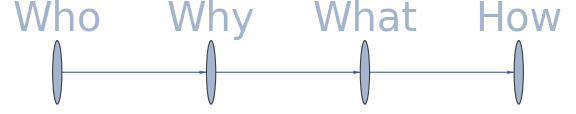

```mathematica
Graph[{"Who"->"Why","Why"->"What","What"->"How"},VertexLabelStyle->Directive[40],
VertexLabels->  Placed["Name",Above],ImageSize->Large]
```

## Anatoly @ Coderbunker July 2017

## Who

### My Languages

Matlab | 20%
\[MathematicaIcon]Mathematica | 5%
.NET | 5%
python | 2%
Natural | remainder

### How to listen to this talk

Ask questions anytime
Hold code suggestions for final 10 minutes

## Why?

```mathematica
list=Import["/Users/Anatoly/Downloads/KzCHMAx.mov","ImageList"];
```

```mathematica
ListAnimate[list,15,AnimationRepetitions->1,AnimationRunning->False]
```

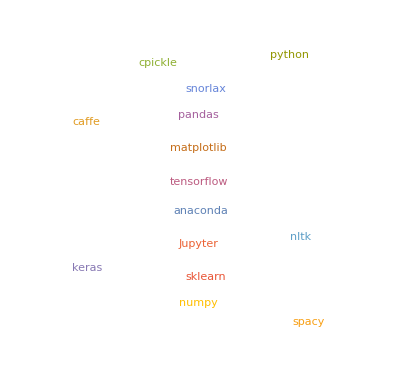

```mathematica
WordCloud[{python, Jupyter, numpy,caffe,
spacy,matplotlib, sklearn,
nltk, pandas, snorlax, anaconda,
keras, tensorflow, cpickle}]
```

## What

### Definition

```mathematica
definition="Mathematica is a system for modern technical computing.";
```

```mathematica
TextStructure[definition,"DependencyGraphs"]
```

{-Graphics-}

### Investigation

```mathematica
WordDefinition["system"][[1]]
```

instrumentality that combines interrelated interacting artifacts designed to work as a coherent entity

```mathematica
TextStructure[%,"DependencyGraphs"]
```

{-Graphics-}

{-Graphics-}

## Alternative Systems Review

System | Scope | Environment
Rapidminer | Narrow | Graphical
Mathematica | General | Notebook
MATLAB + NN toolb ox + ML toolbox | General | Code
python, Jupyter, numpy,caffe,
spacy,matplotlib, sklearn,
nltk, pandas, snorlax, anaconda,
keras, tensorflow, cpickle | General | Code
∨Notebook
Azure ML studio | Narrow | Graphical

## Language

```mathematica
examples={"Logical"->{"Prolog"},"Functional"->{"Julia","Haskell","F#"},"Symbolic"->{"Maple","SymPy"}};
```

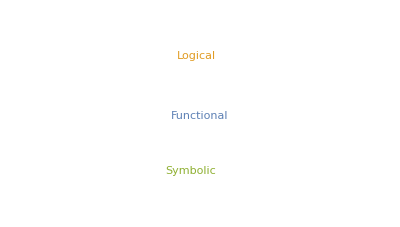

```mathematica
WordCloud[Keys[examples]]
```

## Environment

Notebook Front End + Kernel
Started in V1 in 1988

Alternative Eclipse-based

## Deep Learning in 5 lines

### Get images from Bing

```mathematica
allData=Map[Thread[WebImageSearch[#,"Thumbnails"]->#]&,{"cat","dog"}]
```

{{-Graphics-→cat,-Graphics-→cat,-Graphics-→cat,-Graphics-→cat,-Graphics-→cat,-Graphics-→cat,-Graphics-→cat,-Graphics-→cat,-Graphics-→cat,-Graphics-→cat},{-Graphics-→dog,-Graphics-→dog,-Graphics-→dog,-Graphics-→dog,-Graphics-→dog,-Graphics-→dog,-Graphics-→dog,-Graphics-→dog,-Graphics-→dog,-Graphics-→dog}}

### Train the model

```mathematica
classifier = Classify[Flatten[allData[[All,;;4]]]]
```

ClassifierFunction[…]

### Evaluate the model

```mathematica
measurements=ClassifierMeasurements[classifier,Flatten[allData],"Accuracy"]
```

0.95

### Explore

```mathematica
Manipulate[classifier[image,"Probabilities"],{image,Keys[measurements["WorstClassifiedExamples"->5]]}]
```

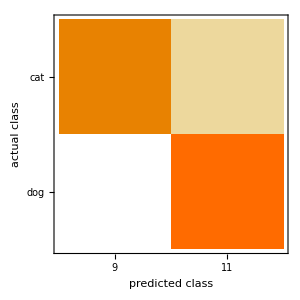

```mathematica
measurements["ConfusionMatrixPlot"]
```

### Backup

```mathematica
allData={{-Graphics-->"cat",-Graphics-->"cat",-Graphics-->"cat",-Graphics-->"cat",-Graphics-->"cat",-Graphics-->"cat",-Graphics-->"cat",-Graphics-->"cat",-Graphics-->"cat",-Graphics-->"cat"},{-Graphics-->"dog",-Graphics-->"dog",-Graphics-->"dog",-Graphics-->"dog",-Graphics-->"dog",-Graphics-->"dog",-Graphics-->"dog",-Graphics-->"dog",-Graphics-->"dog",-Graphics-->"dog"}};
```

## Dimension Reduction

### Flags

```mathematica
FeatureSpacePlot[EntityValue["Country","FlagImage"]]
```

-Graphics-

### Concepts

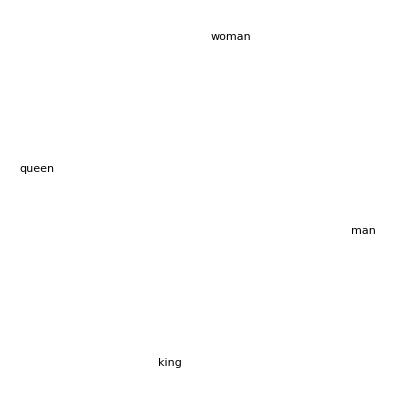

```mathematica
FeatureSpacePlot[{"man","woman","king","queen"}]
```

## Fast.ai Lesson 1

### Get a pre-trained model

```mathematica
net=NetModel["Wolfram ImageIdentify Net for WL 11.1"]
```

NetChain[]

```mathematica
Manipulate[net[image],{image,RandomSample[Keys[Flatten[allData]],5]}]
```

```mathematica
net[Keys[Flatten[allData]]]
```

{domestic cat,European wildcat,domestic cat,domestic cat,domestic cat,bobcat,domestic cat,domestic cat,shoebox,domestic cat,kit fox,Labrador retriever,German shepherd,Cardigan Welsh corgi,Alaskan malamute,Labrador retriever,English cocker spaniel,dachshund,golden retriever,chow chow}

### Fine tune the model

```mathematica
encoder=net[["Input"]];
decoder=NetDecoder[{"Class",{"cat","dog"}}];
```

```mathematica
catNet=NetChain[Append[Drop[Normal[net],-2],{"linear"->LinearLayer[],"softmax"->SoftmaxLayer[]}],"Input"->encoder,"Output"->decoder]
```

NetChain[]

```mathematica
catNet=NetTrain[catNet,Flatten[allData[[All,;;4]]],ValidationSet->Scaled[0.3]];
```

### Evaluate

```mathematica
measurements=ClassifierMeasurements[Classify[catNet],Flatten[allData]]
```

ClassifierMeasurementsObject[…]

```mathematica
Manipulate[catNet[image,"Probabilities"],{image,Keys[measurements["WorstClassifiedExamples"->5]]}]
```

## Summary

### Mathematica is a system for technical computing, including deep learning

Language excels in support for symbolic, functional and rule-based programming
Large number of curated algorithms built-in
Advanced notebook interface (Jupyter N+2)
Seamless integration between different functionality

### Is great for

When you value cycle-time above all (R&D tasks)
Projects that use algorithms / data from vastly different areas

### Possibly not best choice for

Massive scale,  large datasets
Careful control of data type, bit resolution
When parallel threading is important
When want to use code from last month’s paper